Autor: Krzysztof Dragon

# Metody numeryczne w technice

## (kierunek informatyka)

## Projekt 5

Metoda kolejnych przybliżeń

## Równanie Fredholma II rodzaju

### Zadanie 1

Wyznaczyć metodą kolejnych przybliżeń rozwiązanie przybliżone y_n równania

y(x)=ⅇ^x-1/4∫_0^1 (x ⅇ^t y(t))ⅆt

Argument:  n

Sprawdzić, czy metodę można zastosować. 
Wyznaczyć rozwiązanie dla kilku wartości n. 
Na tej podstawie odgadnąć rozwiązanie dokładne i sprawdzić jego poprawność.

### Zadanie 2

Wyznaczyć rozwiązania przybliżone y_n dla  n=2,4,6,8, równania:

y(x)=sin x + (x-1)/4+1/4∫_0^(π/2) (t-x)  y(t)ⅆt.

Utworzyć wykresy porównujące rozwiązanie przybliżone z rozwiązaniem dokładnym, którym jest funkcja y(x)=sin x, np.  w postaci:

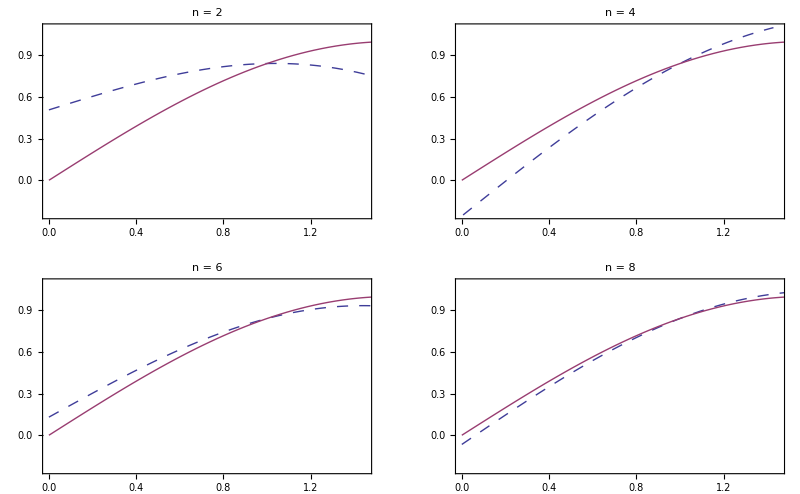

```mathematica
Clear[mkpf2];
mkpf2[k_,f_,a_,b_,λ_,n_,z_Symbol] := Module[{ϕ,i, wyn=0,x,t},
(* Definicja funkcji ϕ *)
ϕ[0][x_] := f[x];
Do[ϕ[i][x_]=Integrate[k[x,t]*ϕ[i-1][t],{t,a,b}],{i,1,n}];
(* Utworzenie rozwiązania przybliżonego *)
Do[wyn=wyn+λ^i*ϕ[i][z],{i,0,n}];
(* Wypisanie rozwiązania przybliżonego *)
Return[wyn]
];
```

```mathematica
(* Zadanie 1 *)
(* Sprawdzam,czy metodę można zastosować *)
a=0;
b=1;
λ = -1/4;
f[x_] := ⅇ^x;
k[x_,t_] := x* ⅇ^t;

M =MaxValue[{x* ⅇ^t,{0 <= x <= 1,0<=t<=1}},{x,t}];

Abs[λ] < 1/(M(b-a)) (* Jeżeli jest True to możemy zastosować metodę *)
```

True

```mathematica
(* n = 10 *)
n = 10;
mkpf2[k,f,a,b,λ,n, x]
```

ⅇ^x-(209715 (-1+ⅇ^2) x)/2097152

```mathematica
(* n = 20 *)
n = 20;
mkpf2[k,f,a,b,λ,n, x]
```

ⅇ^x-(219902325555 (-1+ⅇ^2) x)/2199023255552

```mathematica
(* n = 50 *)
n = 50;
mkpf2[k,f,a,b,λ,n, x]
```

ⅇ^x-(253530120045645880299340641075 (-1+ⅇ^2) x)/2535301200456458802993406410752

```mathematica
(* n = 1000 *)
n = 1000;
mkpf2[k,f,a,b,λ,n, x];
```

ⅇ^x-(22962613905485090484656664023553639680446354041773904009552854736515325227847406277133189726330125398368919292779749255468942379217261106628518627123333063707825997829062456000137755829648008974285785398012697248956323092729277672789463405208093270794180999311632479761788925921124662329907232844394066536268833781796891701120475896961582811780186955300085800543341325166104401626447256258352253576663441319799079283625404355971680808431970636650308177886780418384110991556717934407832016391443326116551076085116745203105669757283886410901783055156776525035087105760164568554163593090752436970229805875 (-1+ⅇ^2) x)/229626139054850904846566640235536396804463540417739040095528547365153252278474062771331897263301253983689192927797492554689423792172611066285186271233330637078259978290624560001377558296480089742857853980126972489563230927292776727894634052080932707941809993116324797617889259211246623299072328443940665362688337817968917011204758969615828117801869553000858005433413251661044016264472562583522535766634413197990792836254043559716808084319706366503081778867804183841109915567179344078320163914433261165510760851167452031056697572838864109017830551567765250350871057601645685541635930907524369702298058752

```mathematica
(* Odgaduję rozwiązanie dokładne: y = ⅇ^x-((-1+ⅇ^2) x)/10;*)
```

```mathematica
(* Sprawdzam dokładność *)
```

```mathematica
g[x_] := ⅇ^x-((-1+ⅇ^2) x)/10;
```

```mathematica
g[x] == ⅇ^x-1/4∫_0^1 (x ⅇ^t g[t])ⅆt // Simplify (* Jeżeli zwróci True to odgadnięte rozwiązanie jest rozwiązaniem dokładnym*)
```

True

```mathematica
(* Zadanie 2 *)
y[x]=Sin[x] + (x-1)/4+1/4∫_0^(π/2) (t-x)  y[t]ⅆt;
(* Funkcja dokładna *)
```

```mathematica
g[x]=Sin[x];

(* Wyniki dla n = 2,4,6,8 *)
Clear[a,b,λ,f,k, M]
(* Sin[x] + (x-1)/4+1/4∫_0^(π/2) (t-x)y[t]ⅆt *)
a=0;
b=π/2;
λ = 1/4;
f[x_] := Sin[x] + (x-1)/4;
k[x_,t_] := (t-x);

M = MaxValue[{t-x,0<=t<=π/2},{x,t}]
Abs[λ] < 1/(M(b-a)) (* Jeżeli jest True to możemy zastosować metodę *)
```

∞

False

```mathematica
n2 = mkpf2[k,f,a,b,λ,2, x] // Simplify
n4 = mkpf2[k,f,a,b,λ,4, x]// Simplify
n6 = mkpf2[k,f,a,b,λ,6, x]// Simplify
n8 = mkpf2[k,f,a,b,λ,8, x]// Simplify
```

(32 π^3+3072 (-1+x)-π^4 (-1+x)+384 π x-96 π^2 (1+x))/12288

(98304 π^3-32 π^7+9437184 (-1+x)-3072 π^4 (-1+x)+π^8 (-1+x)+1179648 π x-384 π^5 x-294912 π^2 (1+x)+96 π^6 (1+x))/37748736

1/115964116992(301989888 π^3-98304 π^7+32 π^11+28991029248 (-1+x)-9437184 π^4 (-1+x)+3072 π^8 (-1+x)-π^12 (-1+x)+3623878656 π x-1179648 π^5 x+384 π^9 x-905969664 π^2 (1+x)+294912 π^6 (1+x)-96 π^10 (1+x))

1/356241767399424(927712935936 π^3-301989888 π^7+98304 π^11-32 π^15+89060441849856 (-1+x)-28991029248 π^4 (-1+x)+9437184 π^8 (-1+x)-3072 π^12 (-1+x)+π^16 (-1+x)+11132555231232 π x-3623878656 π^5 x+1179648 π^9 x-384 π^13 x-2783138807808 π^2 (1+x)+905969664 π^6 (1+x)-294912 π^10 (1+x)+96 π^14 (1+x))

```mathematica
p1 = Plot[{n2,Sin[x]},{x,0,π/2}, PlotLabel->"n = 2", PlotStyle->{Dashed,Red}];
p2 = Plot[{n4,Sin[x]},{x,0,π/2}, PlotLabel->"n = 4", PlotStyle->{Dashed,Red}];
p3 = Plot[{n6,Sin[x]},{x,0,π/2}, PlotLabel->"n = 6", PlotStyle->{Dashed,Red}];
p4 = Plot[{n8,Sin[x]},{x,0,π/2}, PlotLabel->"n = 8", PlotStyle->{Dashed,Red}];
```

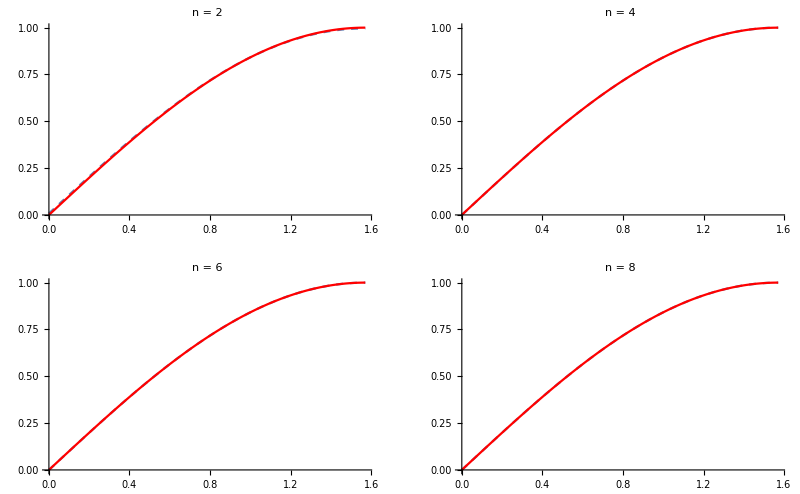

```mathematica
GraphicsGrid[{{p1,p2},{p3,p4}}, Frame -> All]
```